```mathematica
f[x_]:=Cos[2 Pi x]
range={-3, 2, 100};
```

```mathematica
sincn[x_]:=N[Sin[Pi x]/(Pi x)]
```

```mathematica
r1=range[[1]];r2=range[[2]];r3=range[[3]];T=N[(r2-r1)/r3];
sr1=r3/r1;sr2=r3/r2;
Sx=Range[r1, r2, T];
Sy=f/@Sx;
```

```mathematica
{r1, r2, T}
{sr1, sr2}
```

{-3,2,0.05}

{-100/3,50}

```mathematica
(r3/r1)*2
```

-200/3

```mathematica
Manipulate[Plot[{f[x], cft1[Sy][x]}, {x, r1, r2}], {r1}]
```

Plot::plln: Limiting value Null in {x,Null,2} is not a machine-sized real number.

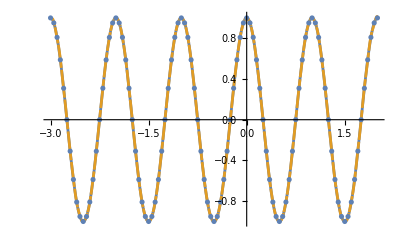

```mathematica
cft1[S_][t_]:=Sum[f[n T]*sincn[(t-n T)/T], {n, -200/3, sr2}]
Show[Plot[{f[x], cft1[Sy][x]}, {x, r1, r2}], ListPlot[Transpose[{Sx, Sy}]]]
```

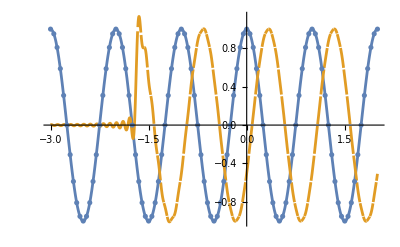

```mathematica
cft2[S_][t_]:=Sum[S[[n-sr1+1]]*sincn[(t-n T)/T], {n, sr1, sr2}]
Show[Plot[{f[x], cft2[Sy][x]}, {x, r1, r2}], ListPlot[Transpose[{Sx, Sy}]]]
```

Dot::dotsh: Tensors {1.,0.951057,0.809017,0.587785,0.309017,-2.44991×10^-15,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,«22»,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,-1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057,«51»} and {0.0103763,-0.0100012,0.00965232,-0.00932694,0.00902278,-0.00873783,0.00847033,-0.00821872,0.00798163,-0.00775783,0.00754624,-0.00734589,«27»,-0.00421354,0.00415033,-0.00408899,0.00402944,-0.0039716,0.0039154,-0.00386076,0.00380763,-0.00375594,0.00370564,-0.00365667,«34»} have incompatible shapes.

Dot::dotsh: Tensors {1.,0.951057,0.809017,0.587785,0.309017,-2.44991×10^-15,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,«22»,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,-1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057,«51»} and {0.0119614,-0.0114946,0.0110628,-0.0106623,0.0102898,-0.00994249,0.00961782,-0.00931369,0.0090282,-0.00875969,0.0085067,-0.00826791,«27»,-0.00462931,0.00455767,-0.00448822,0.00442086,-0.00435548,0.00429201,-0.00423037,0.00417047,-0.00411224,0.00405562,-0.00400053,«34»} have incompatible shapes.

Dot::dotsh: Tensors {1.,0.951057,0.809017,0.587785,0.309017,-2.44991×10^-15,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,«22»,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,-1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057,«51»} and {0.0136188,-0.0130413,0.0125108,-0.0120217,0.0115695,-0.0111501,0.01076,-0.0103962,0.0100563,-0.0097379,0.00943904,-0.00915797,«27»,-0.00499411,0.00491431,-0.00483702,0.00476212,-0.00468951,0.00461908,-0.00455073,0.00448438,-0.00441993,0.00435731,-0.00429644,«34»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

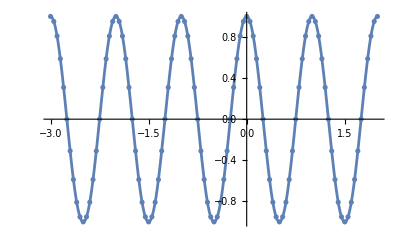

```mathematica
cft3[S_][t_]:=Dot[S, Table[sincn[(t-n T)/T], {n, sr1, sr2}]]
Show[Plot[{f[x], cft3[Sy][x]}, {x, r1, r2}], ListPlot[Transpose[{Sx, Sy}]]]
```

```mathematica
cft4[S_][t_]:=S.Table[sincn[(t/T)-n ], {n, sr1, sr2}]
Show[Plot[{f[x], cft4[Sy][x]}, {x, r1, r2}], ListPlot[Transpose[{Sx, Sy}]]]
```

Dot::dotsh: Tensors {1.,0.951057,0.809017,0.587785,0.309017,-2.44991×10^-15,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,«22»,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,-1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057,«51»} and {0.0103763,-0.0100012,0.00965232,-0.00932694,0.00902278,-0.00873783,0.00847033,-0.00821872,0.00798163,-0.00775783,0.00754624,-0.00734589,«27»,-0.00421354,0.00415033,-0.00408899,0.00402944,-0.0039716,0.0039154,-0.00386076,0.00380763,-0.00375594,0.00370564,-0.00365667,«34»} have incompatible shapes.

Dot::dotsh: Tensors {1.,0.951057,0.809017,0.587785,0.309017,-2.44991×10^-15,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,«22»,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,-1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057,«51»} and {0.0119614,-0.0114946,0.0110628,-0.0106623,0.0102898,-0.00994249,0.00961782,-0.00931369,0.0090282,-0.00875969,0.0085067,-0.00826791,«27»,-0.00462931,0.00455767,-0.00448822,0.00442086,-0.00435548,0.00429201,-0.00423037,0.00417047,-0.00411224,0.00405562,-0.00400053,«34»} have incompatible shapes.

Dot::dotsh: Tensors {1.,0.951057,0.809017,0.587785,0.309017,-2.44991×10^-15,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,«22»,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,-1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057,«51»} and {0.0136188,-0.0130413,0.0125108,-0.0120217,0.0115695,-0.0111501,0.01076,-0.0103962,0.0100563,-0.0097379,0.00943904,-0.00915797,«27»,-0.00499411,0.00491431,-0.00483702,0.00476212,-0.00468951,0.00461908,-0.00455073,0.00448438,-0.00441993,0.00435731,-0.00429644,«34»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

-Graphics-

```mathematica
RepeatedTiming[cft1[Sy][Pi/3]]
RepeatedTiming[cft2[Sy][Pi/3]]
RepeatedTiming[cft3[Sy][Pi/3]]
RepeatedTiming[cft4[Sy][Pi/3]]
```

{0.00055075,0.952197}

{0.000341418,-0.220976}

Dot::dotsh: Tensors {1.,0.951057,0.809017,0.587785,0.309017,-2.44991×10^-15,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,«22»,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,-1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057,«51»} and {0.00448663,-0.00457084,0.00465828,-0.00474912,0.00484358,-0.00494187,0.00504424,-0.00515093,0.00526224,-0.00537846,0.00549993,-0.00562702,«27»,-0.0159401,0.0170566,-0.0183413,0.0198352,-0.021594,0.0236952,-0.0262493,0.0294205,-0.0334633,0.0387942,-0.0461453,«34»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

{0.000273387,{1.,0.951057,0.809017,0.587785,0.309017,-2.44991×10^-15,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,5.51091×10^-16,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,-4.28626×10^-16,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,3.06162×10^-16,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,-1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,6.12323×10^-17,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,6.12323×10^-17,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,-1.83697×10^-16,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,3.06162×10^-16,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,-4.28626×10^-16,0.309017,0.587785,0.809017,0.951057,1.}.{0.00448663,-0.00457084,0.00465828,-0.00474912,0.00484358,-0.00494187,0.00504424,-0.00515093,0.00526224,-0.00537846,0.00549993,-0.00562702,0.00576012,-0.00589966,0.00604614,-0.00620007,0.00636205,-0.00653272,0.0067128,-0.00690308,0.00710447,-0.00731797,0.00754469,-0.00778591,0.00804306,-0.00831778,0.00861193,-0.00892765,0.0092674,-0.00963403,0.0100309,-0.0104618,0.0109314,-0.0114452,0.0120096,-0.0126326,0.0133238,-0.0140949,0.0149609,-0.0159401,0.0170566,-0.0183413,0.0198352,-0.021594,0.0236952,-0.0262493,0.0294205,-0.0334633,0.0387942,-0.0461453,0.0569338,-0.0743061,0.106935,-0.190656,0.878239,0.336954,-0.141359,0.0894409,-0.0654152,0.051564,-0.0425536,0.0362238,-0.0315332,0.0279181,-0.0250467,0.0227109,-0.0207735,0.0191407,-0.0177459,0.0165406,-0.0154885,0.0145624,-0.0137407,0.0130068,-0.0123473,0.0117515,-0.0112105,0.0107171,-0.0102654,0.00985013,-0.0094672,0.00911292,-0.00878421,0.00847838}}

Dot::dotsh: Tensors {1.,0.951057,0.809017,0.587785,0.309017,-2.44991×10^-15,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,«22»,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,-1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057,«51»} and {0.00448663,-0.00457084,0.00465828,-0.00474912,0.00484358,-0.00494187,0.00504424,-0.00515093,0.00526224,-0.00537846,0.00549993,-0.00562702,«27»,-0.0159401,0.0170566,-0.0183413,0.0198352,-0.021594,0.0236952,-0.0262493,0.0294205,-0.0334633,0.0387942,-0.0461453,«34»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

{0.000267112,{1.,0.951057,0.809017,0.587785,0.309017,-2.44991×10^-15,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,5.51091×10^-16,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,-4.28626×10^-16,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,3.06162×10^-16,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,-1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,6.12323×10^-17,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,6.12323×10^-17,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,-1.83697×10^-16,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,3.06162×10^-16,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,-4.28626×10^-16,0.309017,0.587785,0.809017,0.951057,1.}.{0.00448663,-0.00457084,0.00465828,-0.00474912,0.00484358,-0.00494187,0.00504424,-0.00515093,0.00526224,-0.00537846,0.00549993,-0.00562702,0.00576012,-0.00589966,0.00604614,-0.00620007,0.00636205,-0.00653272,0.0067128,-0.00690308,0.00710447,-0.00731797,0.00754469,-0.00778591,0.00804306,-0.00831778,0.00861193,-0.00892765,0.0092674,-0.00963403,0.0100309,-0.0104618,0.0109314,-0.0114452,0.0120096,-0.0126326,0.0133238,-0.0140949,0.0149609,-0.0159401,0.0170566,-0.0183413,0.0198352,-0.021594,0.0236952,-0.0262493,0.0294205,-0.0334633,0.0387942,-0.0461453,0.0569338,-0.0743061,0.106935,-0.190656,0.878239,0.336954,-0.141359,0.0894409,-0.0654152,0.051564,-0.0425536,0.0362238,-0.0315332,0.0279181,-0.0250467,0.0227109,-0.0207735,0.0191407,-0.0177459,0.0165406,-0.0154885,0.0145624,-0.0137407,0.0130068,-0.0123473,0.0117515,-0.0112105,0.0107171,-0.0102654,0.00985013,-0.0094672,0.00911292,-0.00878421,0.00847838}}

```mathematica
Dimensions[Sy]
```

{101}

```mathematica
Dimensions[Table[sincn[(t/T)-n ], {n, sr1, sr2}]]
```

{84}

```mathematica
cft[S_][t_]:=S.Table[sincn[(t/T)-n ], {n, sr1, sr2}]
Show[Plot[{f[x], cft[Sy][x]}, {x, r1, r2}], ListPlot[Transpose[{Sx, Sy}]]]
```

Dot::dotsh: Tensors {1.,0.951057,0.809017,0.587785,0.309017,-2.44991×10^-15,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,«22»,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,-1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057,«51»} and {0.0103763,-0.0100012,0.00965232,-0.00932694,0.00902278,-0.00873783,0.00847033,-0.00821872,0.00798163,-0.00775783,0.00754624,-0.00734589,«27»,-0.00421354,0.00415033,-0.00408899,0.00402944,-0.0039716,0.0039154,-0.00386076,0.00380763,-0.00375594,0.00370564,-0.00365667,«34»} have incompatible shapes.

Dot::dotsh: Tensors {1.,0.951057,0.809017,0.587785,0.309017,-2.44991×10^-15,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,«22»,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,-1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057,«51»} and {0.0119614,-0.0114946,0.0110628,-0.0106623,0.0102898,-0.00994249,0.00961782,-0.00931369,0.0090282,-0.00875969,0.0085067,-0.00826791,«27»,-0.00462931,0.00455767,-0.00448822,0.00442086,-0.00435548,0.00429201,-0.00423037,0.00417047,-0.00411224,0.00405562,-0.00400053,«34»} have incompatible shapes.

Dot::dotsh: Tensors {1.,0.951057,0.809017,0.587785,0.309017,-2.44991×10^-15,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,«22»,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,-1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057,«51»} and {0.0136188,-0.0130413,0.0125108,-0.0120217,0.0115695,-0.0111501,0.01076,-0.0103962,0.0100563,-0.0097379,0.00943904,-0.00915797,«27»,-0.00499411,0.00491431,-0.00483702,0.00476212,-0.00468951,0.00461908,-0.00455073,0.00448438,-0.00441993,0.00435731,-0.00429644,«34»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

-Graphics-